### Tests - students must run these tests

#### data needed for testing - execute this cell!!!

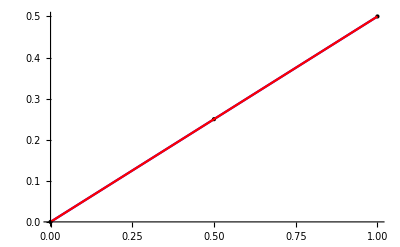
```mathematica
test1={{{0.,0.},{0.5,0.25},{1.,0.5}},-Graphics-,1.118033988749895,1.118033988749895};
```

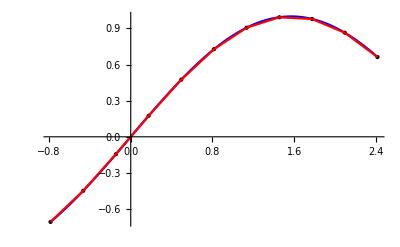
```mathematica
test2={{{-0.7853981633974483,-0.7071067811865476},{-0.4651973737046424,-0.44859920958371774},{-0.14499658401183657,-0.1444890495692213},{0.17520420568096928,0.17430922071549282},{0.49540499537377514,0.4753879955601162},{0.815605785066581,0.7281409538757885},{1.1358065747593868,0.9068743608505455},{1.4560073644521925,0.9934189780649787},{1.7762081541449986,0.9789770669726084},{2.0964089438378046,0.8650167276354797},{2.4166097335306103,0.6631226582407952}},-Graphics-,3.8897620554673584,3.892908022075225};
```

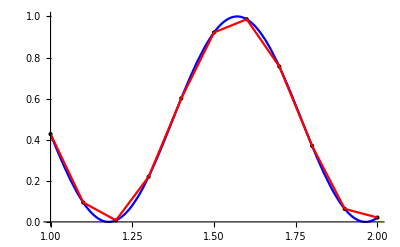
```mathematica
test3={{{1.,0.4272499830956933},{1.1,0.09445349296917202},{1.2,0.007656072102936515},{1.3,0.2195078712863856},{1.4,0.6015024319093752},{1.5,0.9219269793662459},{1.6,0.9864162828487176},{1.7000000000000002,0.7558519962265737},{1.8,0.3700913218931221},{1.9,0.06313150849445992},{2.,0.021170259838307684}},-Graphics-,2.644815439463879,2.722975032935951};
```

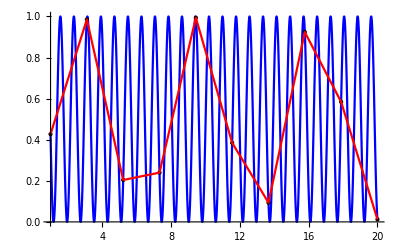
```mathematica
test4={{{1.,0.4272499830956933},{3.111111111111111,0.9852075291245789},{5.222222222222222,0.20392550438158494},{7.333333333333334,0.23984984315876534},{9.444444444444445,0.9938244253295057},{11.555555555555555,0.38477561705909125},{13.666666666666668,0.09376196671512195},{15.777777777777779,0.9240212082185577},{17.88888888888889,0.5839235471459937},{20.,0.012185343602381344}},-Graphics-,19.71005174803517,53.33064323612372};
```

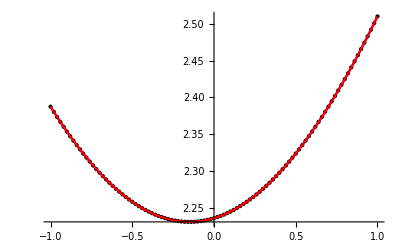
```mathematica
test5={{{-1.,2.3874672772626644},{-0.98,2.380420130985285},{-0.96,2.373520591863487},{-0.94,2.3667699507979223},{-0.92,2.360169485439552},{-0.9,2.353720459187964},{-0.88,2.3474241201793937},{-0.86,2.3412817002659034},{-0.84,2.3352944139872385},{-0.8200000000000001,2.3294634575369493},{-0.8,2.32379000772445},{-0.78,2.318275220934736},{-0.76,2.312920232087566},{-0.74,2.3077261535979523},{-0.72,2.3026940743398807},{-0.7,2.2978250586152114},{-0.6799999999999999,2.293120145129775},{-0.6599999999999999,2.288580345978703},{-0.64,2.2842066456430774},{-0.62,2.2800000000000002},{-0.6,2.2759613353482084},{-0.5800000000000001,2.2720915474513785},{-0.56,2.268391500601252},{-0.54,2.2648620267027306},{-0.52,2.261503924383064},{-0.5,2.258317958127243},{-0.48,2.255304857441672},{-0.45999999999999996,2.252465316048174},{-0.43999999999999995,2.249799991110321},{-0.42000000000000004,2.247309502494038},{-0.4,2.244994432064365},{-0.38,2.2428553230201898},{-0.36,2.240892679268688},{-0.33999999999999997,2.2391069648411173},{-0.31999999999999995,2.2374986033515194},{-0.29999999999999993,2.23606797749979},{-0.28,2.2348154286204487},{-0.26,2.233741256278354},{-0.24,2.232845717912458},{-0.21999999999999997,2.232129028528593},{-0.19999999999999996,2.23159136044214},{-0.17999999999999994,2.2312328430712918},{-0.16000000000000003,2.2310535627814945},{-0.14,2.2310535627814945},{-0.12,2.2312328430712918},{-0.09999999999999998,2.2315913604421396},{-0.07999999999999996,2.232129028528593},{-0.05999999999999994,2.232845717912458},{-0.040000000000000036,2.233741256278354},{-0.020000000000000018,2.2348154286204487},{0.,2.23606797749979},{0.020000000000000018,2.2374986033515194},{0.040000000000000036,2.2391069648411173},{0.06000000000000005,2.240892679268688},{0.08000000000000007,2.2428553230201898},{0.10000000000000009,2.244994432064365},{0.1200000000000001,2.247309502494038},{0.14000000000000012,2.249799991110321},{0.15999999999999992,2.252465316048174},{0.17999999999999994,2.255304857441672},{0.19999999999999996,2.258317958127243},{0.21999999999999997,2.261503924383064},{0.24,2.2648620267027306},{0.26,2.268391500601252},{0.28,2.2720915474513785},{0.30000000000000004,2.2759613353482084},{0.32000000000000006,2.2800000000000002},{0.3400000000000001,2.2842066456430774},{0.3600000000000001,2.288580345978703},{0.3800000000000001,2.293120145129775},{0.40000000000000013,2.2978250586152114},{0.41999999999999993,2.3026940743398807},{0.43999999999999995,2.3077261535979523},{0.45999999999999996,2.3129202320875657},{0.48,2.318275220934736},{0.5,2.32379000772445},{0.52,2.3294634575369497},{0.54,2.3352944139872385},{0.56,2.3412817002659034},{0.5800000000000001,2.3474241201793937},{0.6000000000000001,2.353720459187964},{0.6200000000000001,2.360169485439552},{0.6400000000000001,2.3667699507979223},{0.6600000000000001,2.3735205918634876},{0.6799999999999999,2.3804201309852844},{0.7,2.3874672772626644},{0.72,2.3946607275353227},{0.74,2.4019991673603887},{0.76,2.4094812719753604},{0.78,2.4171057072457547},{0.8,2.4248711305964283},{0.8200000000000001,2.432776191925595},{0.8400000000000001,2.440819534500656},{0.8600000000000001,2.4489997958350265},{0.8800000000000001,2.457315608545227},{0.9000000000000001,2.4657656011875906},{0.9199999999999999,2.4743483990739863},{0.94,2.4830626250660695},{0.96,2.4919069003476033},{0.98,2.500879845174494},{1.,2.5099800796022267}},-Graphics-,2.0613236753934014,2.0613280617948853};
```

#### code needed for testing - execute this cell!!!

```mathematica
errorMsgHW2= {     " 1) make sure you RETURN the answer - it should not be printed with Print [..] \n",
     	 " 2) check  that the order (and structure) of the parameters is correct \n" ,
 " 3) check  that the order (and structure) of the returned values is correct\n" };
```

```mathematica
printError[msg_]:= Print @@ Join[{msg <> "\n"}, errorMsgHW2]
```

```mathematica
testlongestPrimeSum[upper_,  answer_]:= 
Module[{res, checkMore = True, sum},
res=longestPrimeSum[upper] ;
If[  !SameQ[Head[res], List],
	printError["ERROR - function does not return a list"];
	checkMore = False
];
If[  checkMore && (Length[res] ≠ 3 || Length[Select[res, NumericQ]]≠ 3),
printError["ERROR - function does not return correct number or type of elements in the list"];
checkMore = False
];
(* now check actual results *)
If[ checkMore && (res[[2]] ≠  answer),
printError ["Number of terms to add up is incorrect should be " <> ToString[answer]];
checkMore = False
];
If [checkMore,
sum = Sum[Prime[i], {i, res[[1]], res[[1]]+res[[2]]-1}];
];
If [checkMore &&  ! SameQ[sum, res[[3]]],
printError ["The sum is not correct for your starting value and number of terms"];
checkMore = False
];
If [ checkMore && (! PrimeQ[res[[3]]] || res[[3]] ≥ upper),
printError ["The sum is not prime or it is not less than upper"];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testlongestPrimeSum[upper_,  answer_, res_]:= 
Module[{ checkMore = True, sum},
If[  !SameQ[Head[res], List],
	printError["ERROR - function does not return a list"];
	checkMore = False
];
If[  checkMore && (Length[res] ≠ 3 || Length[Select[res, NumericQ]]≠ 3),
printError["ERROR - function does not return correct number or type of elements in the list"];
checkMore = False
];
(* now check actual results *)
If[ checkMore && (res[[2]] ≠  answer),
printError ["Number of terms to add up is incorrect should be " <> ToString[answer]];
checkMore = False
];
If [checkMore,
sum = Sum[Prime[i], {i, res[[1]], res[[1]]+res[[2]]-1}];
];
If [checkMore &&  ! SameQ[sum, res[[3]]],
printError ["The sum is not correct for your starting value and number of terms"];
checkMore = False
];
If [ checkMore && (! PrimeQ[res[[3]]] || res[[3]] ≥ upper),
printError ["The sum is not prime or it is not less than upper"];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testfindPoints[fgh_, int_, pcs_, answer_, precision_]:= 
Module[{res, checkMore = True, sum},
Print["Testing findPoints"];
res=findPoints[fgh,int, pcs] ;
If[  !SameQ[Head[res], List],
	printError["ERROR - function does not return a list"];
	checkMore = False
];
If[  checkMore && (Length[res] ≠ pcs+1 || Length[Select[Flatten[res], NumericQ]]≠ 2 (pcs+1)),
printError["ERROR - function does not return correct number or type of elements in the list"];
checkMore = False
];
(* now check actual results *)
If[ checkMore && Max[Table[EuclideanDistance[res[[i]], answer[[i]]],{i, 1, Length[res]}]] > 10^-precision,
printError ["Incorrect results; correct result is " <> ToString[answer]];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testshowLinesegments[fgh_, int_, pcs_, answer_]:= 
Module[{res, checkMore = True, sum},
Print["Testing showLinesegments"];
res=showLinesegments[fgh,int, pcs] ;
If[  !SameQ[Head[res], Graphics],
	printError["ERROR - function does not return a graphics"];
	checkMore = False
];
If [checkMore,
Print["Compare to correct answer {right: yours; left: correct}"];
Return[{res, answer}],
Return[1]
];
];
```

```mathematica
testlengthOfCurve[fgh_, int_, pcs_, answer_, precision_]:= 
Module[{res, checkMore = True, sum},
Print["Testing lengthOfCurve"];
res=lengthOfCurve[fgh,int, pcs] ;
If[  !SameQ[Head[res], Real],
	printError["ERROR - function does not return an approximate value"];
	checkMore = False
];
(* now check actual results *)
If[ checkMore && Abs[answer-res] > 10^-precision,
printError ["Incorrect results; correct result is " <> ToString[answer]];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testprecisionLength[fgh_, int_, pcs_, answer_, precision_]:= 
Module[{res, checkMore = True, sum},
Print["Testing preciselengthOfCurve"];
res=preciselengthOfCurve[fgh,int, pcs] ;
If[  !SameQ[Head[res], Real],
	printError["ERROR - function does not return an approximate value"];
	checkMore = False
];
(* now check actual results *)
If[ checkMore && Abs[answer-res] > 10^-precision,
printError ["Incorrect results; correct result is " <> ToString[answer]];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testfindPoints[fgh_, int_, pcs_, answer_, precision_, res_]:= 
Module[{ checkMore = True, sum},
Print["Testing findPoints"];
(*res=findPoints[fgh,int, pcs] ;
*)If[  !SameQ[Head[res], List],
	printError["ERROR - function does not return a list"];
	checkMore = False
];
If[  checkMore && (Length[res] ≠ pcs+1 || Length[Select[Flatten[res], NumericQ]]≠ 2 (pcs+1)),
printError["ERROR - function does not return correct number or type of elements in the list"];
checkMore = False
];
(* now check actual results *)
If[ checkMore && Max[Table[EuclideanDistance[res[[i]], answer[[i]]],{i, 1, Length[res]}]] > 10^-precision,
printError ["Incorrect results; correct result is " <> ToString[answer]];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testshowLinesegments[fgh_, int_, pcs_, answer_, res_]:= 
Module[{ checkMore = True, sum},
Print["Testing showLinesegments"];
(*res=showLinesegments[fgh,int, pcs] ;*)
If[  !SameQ[Head[res], Graphics],
	printError["ERROR - function does not return a graphics"];
	checkMore = False
];
If [checkMore,
Print["Compare to correct answer {right: yours; left: correct}"];
Return[{res, answer}],
Return[1]
];
];
```

```mathematica
testlengthOfCurve[fgh_, int_, pcs_, answer_, precision_, res_]:= 
Module[{ checkMore = True, sum},
Print["Testing lengthOfCurve"];
(*res=lengthOfCurve[fgh,int, pcs] ;*)
If[  !SameQ[Head[res], Real],
	printError["ERROR - function does not return an approximate value"];
	checkMore = False
];
(* now check actual results *)
If[ checkMore && Abs[answer-res] > 10^-precision,
printError ["Incorrect results; correct result is " <> ToString[answer]];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

```mathematica
testprecisionLength[fgh_, int_, pcs_, answer_, precision_, res_]:= 
Module[{checkMore = True, sum},
Print["Testing preciselengthOfCurve"];
(*res=preciselengthOfCurve[fgh,int, pcs] ;*)
If[  !SameQ[Head[res], Real],
	printError["ERROR - function does not return an approximate value"];
	checkMore = False
];
(* now check actual results *)
If[ checkMore && Abs[answer-res] > 10^-precision,
printError ["Incorrect results; correct result is " <> ToString[answer]];
checkMore = False
];
If [checkMore,
Print["Answer correct"];
Return[0],
Return[1]
];
];
```

### Testing - longestPrimeSum

```mathematica
res = longestPrimeSum[160]
testlongestPrimeSum[160, 9, res];
```

{2,9,127}

Answer correct

```mathematica
res = longestPrimeSum[5000]
testlongestPrimeSum[5000, 45, res];
```

{4,45,4651}

Answer correct

```mathematica
res = longestPrimeSum[40]
testlongestPrimeSum[40, 4, res];
```

{1,4,17}

Answer correct

```mathematica
res = longestPrimeSum[790]
testlongestPrimeSum[790, 17, res];
```

{2,17,499}

Answer correct

```mathematica
res = longestPrimeSum[21000]
testlongestPrimeSum[21000, 81, res];
```

{5,81,16823}

Answer correct

```mathematica
res = longestPrimeSum[22000]
testlongestPrimeSum[22000, 85, res];
```

{11,85,21407}

Answer correct

```mathematica
res = longestPrimeSum[50000]
testlongestPrimeSum[50000, 137, res];
```

{2,137,49279}

Answer correct

### Testing - arcLength

#### Test 1

{{0.,0.},{0.5,0.25},{1.,0.5}}

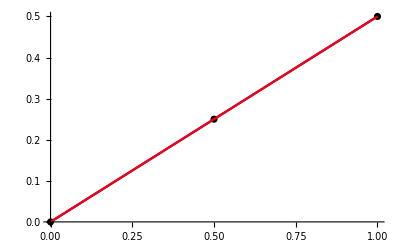

1.11803

$Aborted

```mathematica
testfun[y_]:= 0.5 y;
interval={0., 1};
pieces=2;
precision=7;
(* compute your answer *)
points= findPoints[testfun, interval, pieces]
pic=showLinesegments[testfun, interval, pieces]
length=lengthOfCurve[testfun, interval, pieces]
preclength=preciselengthOfCurve[testfun, interval, precision]
```

```mathematica
(* compare with correct answer *)
testfindPoints[testfun, interval, pieces, test1[[1]], 5, points]
testshowLinesegments[testfun, interval, pieces, test1[[2]], pic]
testlengthOfCurve[testfun, interval, pieces, test1[[3]], 5, length]
testprecisionLength[testfun, interval,pieces,test1[[4]],precision, preclength]
```

Testing findPoints

Answer correct

0

Testing showLinesegments

Compare to correct answer {right: yours; left: correct}

{-Graphics-,-Graphics-}

Testing lengthOfCurve

Answer correct

0

Testing preciselengthOfCurve

Incorrect results; correct result is 1.11803
 1) make sure you RETURN the answer - it should not be printed with Print [..] 
 2) check  that the order (and structure) of the parameters is correct 
 3) check  that the order (and structure) of the returned values is correct

1

#### Test 2

{{-0.785398,-0.707107},{-0.465197,-0.448599},{-0.144997,-0.144489},{0.175204,0.174309},{0.495405,0.475388},{0.815606,0.728141},{1.13581,0.906874},{1.45601,0.993419},{1.77621,0.978977},{2.09641,0.865017},{2.41661,0.663123}}

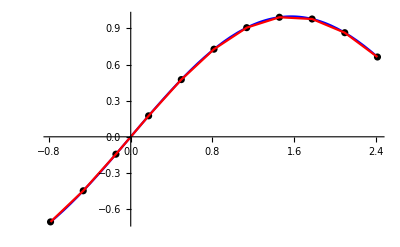

3.88976

3.86334

```mathematica
testfun [x_]:=Sin[x]
interval={-π/4., 10π/13};
pieces=10;
precision=2;
(* compute your answer *)
points= findPoints[testfun, interval, pieces]
pic=showLinesegments[testfun, interval, pieces]
length=lengthOfCurve[testfun, interval, pieces]
preclength=preciselengthOfCurve[testfun, interval, precision]
```

```mathematica
(* compare with correct answer *)
testfindPoints[testfun, interval, pieces, test2[[1]], 5, points]
testshowLinesegments[testfun, interval, pieces, test2[[2]], pic]
testlengthOfCurve[testfun, interval, pieces, test2[[3]], 5, length]
testprecisionLength[testfun, interval,precision,test2[[4]],5, preclength]
```

Testing findPoints

Answer correct

0

Testing showLinesegments

Compare to correct answer {right: yours; left: correct}

{-Graphics-,-Graphics-}

Testing lengthOfCurve

Answer correct

0

Testing preciselengthOfCurve

Incorrect results; correct result is 3.89291
 1) make sure you RETURN the answer - it should not be printed with Print [..] 
 2) check  that the order (and structure) of the parameters is correct 
 3) check  that the order (and structure) of the returned values is correct

1

#### Test 3

{{1.,0.42725},{1.1,0.0944535},{1.2,0.00765607},{1.3,0.219508},{1.4,0.601502},{1.5,0.921927},{1.6,0.986416},{1.7,0.755852},{1.8,0.370091},{1.9,0.0631315},{2.,0.0211703}}

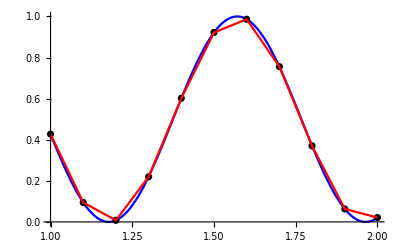

2.64482

2.33994

```mathematica
testfun[z_]:= Cos[4z]^2;
interval={1.,2};
pieces=10;
precision=5;
(* compute your answer *)
points= findPoints[testfun, interval, pieces]
pic=showLinesegments[testfun, interval, pieces]
length=lengthOfCurve[testfun, interval, pieces]
preclength=preciselengthOfCurve[testfun, interval, precision]
```

```mathematica
(* compare with correct answer *)
testfindPoints[testfun, interval, pieces, test3[[1]], 5, points]
testshowLinesegments[testfun, interval, pieces, test3[[2]], pic]
testlengthOfCurve[testfun, interval, pieces, test3[[3]], 5, length]
testprecisionLength[testfun, interval,pieces,test3[[4]],precision, preclength]
```

Testing findPoints

Answer correct

0

Testing showLinesegments

Compare to correct answer {right: yours; left: correct}

{-Graphics-,-Graphics-}

Testing lengthOfCurve

Answer correct

0

Testing preciselengthOfCurve

Incorrect results; correct result is 2.72298
 1) make sure you RETURN the answer - it should not be printed with Print [..] 
 2) check  that the order (and structure) of the parameters is correct 
 3) check  that the order (and structure) of the returned values is correct

1

#### Test 4

{{1.,0.42725},{3.11111,0.985208},{5.22222,0.203926},{7.33333,0.23985},{9.44444,0.993824},{11.5556,0.384776},{13.6667,0.093762},{15.7778,0.924021},{17.8889,0.583924},{20.,0.0121853}}

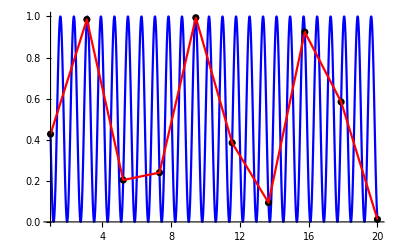

19.7101

19.005

```mathematica
testfun[z_]:= Cos[4z]^2;
interval={1.,20};
pieces=9;
precision=5;
(* compute your answer *)
points= findPoints[testfun, interval, pieces]
pic=showLinesegments[testfun, interval, pieces]
length=lengthOfCurve[testfun, interval, pieces]
preclength=preciselengthOfCurve[testfun, interval, precision]
```

```mathematica
(* compare with correct answer *)
testfindPoints[testfun, interval, pieces, test4[[1]], 5, points]
testshowLinesegments[testfun, interval, pieces, test4[[2]], pic]
testlengthOfCurve[testfun, interval, pieces, test4[[3]], 5, length]
testprecisionLength[testfun, interval,pieces,test4[[4]],precision, preclength]
```

Testing findPoints

Answer correct

0

Testing showLinesegments

Compare to correct answer {right: yours; left: correct}

{-Graphics-,-Graphics-}

Testing lengthOfCurve

Answer correct

0

Testing preciselengthOfCurve

Incorrect results; correct result is 53.3306
 1) make sure you RETURN the answer - it should not be printed with Print [..] 
 2) check  that the order (and structure) of the parameters is correct 
 3) check  that the order (and structure) of the returned values is correct

1

#### Test 5

{{-1.,2.38747},{-0.98,2.38042},{-0.96,2.37352},{-0.94,2.36677},{-0.92,2.36017},{-0.9,2.35372},{-0.88,2.34742},{-0.86,2.34128},{-0.84,2.33529},{-0.82,2.32946},{-0.8,2.32379},{-0.78,2.31828},{-0.76,2.31292},{-0.74,2.30773},{-0.72,2.30269},{-0.7,2.29783},{-0.68,2.29312},{-0.66,2.28858},{-0.64,2.28421},{-0.62,2.28},{-0.6,2.27596},{-0.58,2.27209},{-0.56,2.26839},{-0.54,2.26486},{-0.52,2.2615},{-0.5,2.25832},{-0.48,2.2553},{-0.46,2.25247},{-0.44,2.2498},{-0.42,2.24731},{-0.4,2.24499},{-0.38,2.24286},{-0.36,2.24089},{-0.34,2.23911},{-0.32,2.2375},{-0.3,2.23607},{-0.28,2.23482},{-0.26,2.23374},{-0.24,2.23285},{-0.22,2.23213},{-0.2,2.23159},{-0.18,2.23123},{-0.16,2.23105},{-0.14,2.23105},{-0.12,2.23123},{-0.1,2.23159},{-0.08,2.23213},{-0.06,2.23285},{-0.04,2.23374},{-0.02,2.23482},{0.,2.23607},{0.02,2.2375},{0.04,2.23911},{0.06,2.24089},{0.08,2.24286},{0.1,2.24499},{0.12,2.24731},{0.14,2.2498},{0.16,2.25247},{0.18,2.2553},{0.2,2.25832},{0.22,2.2615},{0.24,2.26486},{0.26,2.26839},{0.28,2.27209},{0.3,2.27596},{0.32,2.28},{0.34,2.28421},{0.36,2.28858},{0.38,2.29312},{0.4,2.29783},{0.42,2.30269},{0.44,2.30773},{0.46,2.31292},{0.48,2.31828},{0.5,2.32379},{0.52,2.32946},{0.54,2.33529},{0.56,2.34128},{0.58,2.34742},{0.6,2.35372},{0.62,2.36017},{0.64,2.36677},{0.66,2.37352},{0.68,2.38042},{0.7,2.38747},{0.72,2.39466},{0.74,2.402},{0.76,2.40948},{0.78,2.41711},{0.8,2.42487},{0.82,2.43278},{0.84,2.44082},{0.86,2.449},{0.88,2.45732},{0.9,2.46577},{0.92,2.47435},{0.94,2.48306},{0.96,2.49191},{0.98,2.50088},{1.,2.50998}}

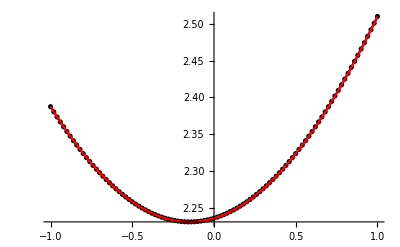

2.06132

2.05808

```mathematica
testfun[z_]:= √(5+ .3z+z^2);
interval={-1.,1};
pieces=100;
precision=5;
(* compute your answer *)
points= findPoints[testfun, interval, pieces]
pic=showLinesegments[testfun, interval, pieces]
length=lengthOfCurve[testfun, interval, pieces]
preclength=preciselengthOfCurve[testfun, interval, precision]
```

```mathematica
(* compare with correct answer *)
testfindPoints[testfun, interval, pieces, test5[[1]], 5, points]
testshowLinesegments[testfun, interval, pieces, test5[[2]], pic]
testlengthOfCurve[testfun, interval, pieces, test5[[3]], 5, length]
testprecisionLength[testfun, interval,pieces,test5[[4]],precision, preclength]
```

Testing findPoints

Answer correct

0

Testing showLinesegments

Compare to correct answer {right: yours; left: correct}

{-Graphics-,-Graphics-}

Testing lengthOfCurve

Answer correct

0

Testing preciselengthOfCurve

Incorrect results; correct result is 2.06133
 1) make sure you RETURN the answer - it should not be printed with Print [..] 
 2) check  that the order (and structure) of the parameters is correct 
 3) check  that the order (and structure) of the returned values is correct

1